# Sprott: Bulk Implementation

The idea is to implement some standard tools for all the ODEs from Sprott.  Here are all the functions, parameters and IC.  I made all of them have parameters a, b, c, d, and the smoothing parameter m. The order and names may not match your choices.

```mathematica
Clear[Sprott,Di,Rd,Sa,Sg,He]
Sprott=<|
1-><|"fun" :>-a ypp+b yp-c y+d yp^2,"par"->{2.017,0,1,1,50},"IC"->{0,0,1}|>,2-><|"fun" :>a ypp-b yp+c y+d y^2,"par"->{0,2.8,1,1,50},"IC"->{-0.5,-1,1}|>,3-><|"fun" :>-a ypp-b yp+c y+d (y^2-1),"par"->{0.44,2,0,1,50},"IC"->{0,0,0}|>,4-><|"fun" :>-a ypp-b yp+c y+d y^2,"par"->{0.5,1,1,1,50},"IC"->{0,1,0}|>,5-><|"fun" :>a ypp-b yp+c y+d (Abs[y]-1),"par"->{0,2,0,1,50},"IC"->{-1,-1,1}|>,6-><|"fun" :>-a ypp-b yp+c y+d (Abs[y]-1),"par"->{0.6,1,0,1,50},"IC"->{0,0,0}|>,7-><|"fun" :>-a ypp-b yp+c y-d (Di[y]-1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0}|>,8-><|"fun" :>-a ypp-b yp+c y-d (Rd[y]+1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0}|>,9-><|"fun" :>a ypp-b yp+c y-d (Di[y]-1),"par"->{0,2.9,0.7,1,50},"IC"->{0,-0.5,0.5}|>,10-><|"fun" :>a ypp-b yp+c y-d (Rd[y]+1),"par"->{0,2.9,0.7,1,50},"IC"->{0,0.5,-0.5}|>,11-><|"fun" :>-a ypp-b yp-c y+d Sg[m][y],"par"->{0.5,1,1,1,50},"IC"->{0,1,0}|>,12-><|"fun" :>-a ypp-b yp+c y-d Sg[m][y],"par"->{0.5,1,1,1,50},"IC"->{0,1,0}|>,13-><|"fun" :>-a ypp-b yp-c y+d He[m][y],"par"->{0.7,1,1,1,50},"IC"->{0,1,0}|>,14-><|"fun" :>-a ypp-b yp-c y+d Sa[y],"par"->{0.4,1,1,2,50},"IC"->{0,1,0}|>,15-><|"fun" :>-a ypp-b yp+c y-d Sa[y],"par"->{0.4,1,1,2,50},"IC"->{0,1,0}|>,16-><|"fun" :>-a ypp-b yp-c y+d Tanh[y],"par"->{0.19,1,1,2,50},"IC"->{0,1,0}|>,17-><|"fun" :>-a ypp-b yp+c y-d Tanh[y],"par"->{0.19,1,1,2,50},"IC"->{0,1,0}|>,18-><|"fun" :>a ypp-b yp+c y-d y^3,"par"->{0,3.7,1,1,50},"IC"->{0,0.5,1}|>,19-><|"fun" :>-a ypp+b yp-c y-d yp^3,"par"->{0.6,2.8,1,1,50},"IC"->{0,1,0}|>,20-><|"fun" :>-a ypp-b yp+c y-d y^3,"par"->{0.7,1,1,1,50},"IC"->{0,1,0}|>,21-><|"fun" :>-a ypp-b yp-c y+d y^3,"par"->{0.35,1,1,1,50},"IC"->{0,1,0}|>,22-><|"fun" :>-a ypp-b yp+c y+d Sin[y],"par"->{0.2,1,0,1,50},"IC"->{0,1,0}|>|>;
(* Compute Derivtives automatically *)
NewSprott=Map[Function[entry,With[{der=D[entry["fun"],{{y,yp,ypp}}]},Append[entry,"der":>der]]],Sprott];
DerSub={Abs'[y]->Absp[y],Di'[y]->Dip[y],Rd'[y]->Rdp[y],Sa'[y]->Sap[y],Sg[m]'[y]->Sgp[m][y],He[m]'[y]->He[m][y]};
NewSprott=NewSprott/.DerSub
```

<|1→<|fun:>-a ypp+b yp-c y+d yp^2,par→{2.017,0,1,1,50},IC→{0,0,1},der:>{-c,b+2 d yp,-a}|>,2→<|fun:>a ypp-b yp+c y+d y^2,par→{0,2.8,1,1,50},IC→{-0.5,-1,1},der:>{c+2 d y,-b,a}|>,3→<|fun:>-a ypp-b yp+c y+d (y^2-1),par→{0.44,2,0,1,50},IC→{0,0,0},der:>{c+2 d y,-b,-a}|>,4→<|fun:>-a ypp-b yp+c y+d y^2,par→{0.5,1,1,1,50},IC→{0,1,0},der:>{c+2 d y,-b,-a}|>,5→<|fun:>a ypp-b yp+c y+d (Abs[y]-1),par→{0,2,0,1,50},IC→{-1,-1,1},der:>{c+d Absp[y],-b,a}|>,6→<|fun:>-a ypp-b yp+c y+d (Abs[y]-1),par→{0.6,1,0,1,50},IC→{0,0,0},der:>{c+d Absp[y],-b,-a}|>,7→<|fun:>-a ypp-b yp+c y-d (Di[y]-1),par→{0.3,0.3,0,1,50},IC→{0,0,0},der:>{c-d Dip[y],-b,-a}|>,8→<|fun:>-a ypp-b yp+c y-d (Rd[y]+1),par→{0.3,0.3,0,1,50},IC→{0,0,0},der:>{c-d Rdp[y],-b,-a}|>,9→<|fun:>a ypp-b yp+c y-d (Di[y]-1),par→{0,2.9,0.7,1,50},IC→{0,-0.5,0.5},der:>{c-d Dip[y],-b,a}|>,10→<|fun:>a ypp-b yp+c y-d (Rd[y]+1),par→{0,2.9,0.7,1,50},IC→{0,0.5,-0.5},der:>{c-d Rdp[y],-b,a}|>,11→<|fun:>-a ypp-b yp-c y+d Sg[m][y],par→{0.5,1,1,1,50},IC→{0,1,0},der:>{-c+d Sgp[m][y],-b,-a}|>,12→<|fun:>-a ypp-b yp+c y-d Sg[m][y],par→{0.5,1,1,1,50},IC→{0,1,0},der:>{c-d Sgp[m][y],-b,-a}|>,13→<|fun:>-a ypp-b yp-c y+d He[m][y],par→{0.7,1,1,1,50},IC→{0,1,0},der:>{-c+d He[m][y],-b,-a}|>,14→<|fun:>-a ypp-b yp-c y+d Sa[y],par→{0.4,1,1,2,50},IC→{0,1,0},der:>{-c+d Sap[y],-b,-a}|>,15→<|fun:>-a ypp-b yp+c y-d Sa[y],par→{0.4,1,1,2,50},IC→{0,1,0},der:>{c-d Sap[y],-b,-a}|>,16→<|fun:>-a ypp-b yp-c y+d Tanh[y],par→{0.19,1,1,2,50},IC→{0,1,0},der:>{-c+d Sech[y]^2,-b,-a}|>,17→<|fun:>-a ypp-b yp+c y-d Tanh[y],par→{0.19,1,1,2,50},IC→{0,1,0},der:>{c-d Sech[y]^2,-b,-a}|>,18→<|fun:>a ypp-b yp+c y-d y^3,par→{0,3.7,1,1,50},IC→{0,0.5,1},der:>{c-3 d y^2,-b,a}|>,19→<|fun:>-a ypp+b yp-c y-d yp^3,par→{0.6,2.8,1,1,50},IC→{0,1,0},der:>{-c,b-3 d yp^2,-a}|>,20→<|fun:>-a ypp-b yp+c y-d y^3,par→{0.7,1,1,1,50},IC→{0,1,0},der:>{c-3 d y^2,-b,-a}|>,21→<|fun:>-a ypp-b yp-c y+d y^3,par→{0.35,1,1,1,50},IC→{0,1,0},der:>{-c+3 d y^2,-b,-a}|>,22→<|fun:>-a ypp-b yp+c y+d Sin[y],par→{0.2,1,0,1,50},IC→{0,1,0},der:>{c+d Cos[y],-b,-a}|>|>

Define the defined  functions and their derivatives

```mathematica
Clear[Di,Dip,Rd,Rdp,Sa,Sap,Sg,Sgp,He,HEp,Absp,m]
Di[u_]:=Max[u,0]; Dip[u_]:=If[u>0,1,0]
Rd[u_]:=Min[u,0]; Rdp[u_]:=If[u<0,1,0]
Sa[u_]:=Piecewise[{ {-1, u<-1},{u, -1<u<1},{1,True}}]; Sap[u_]:=If[Abs[u]<1,1,0]
Sg[m_][u_]:=Tanh[m u]; Sgp[m_][u_]:=m Sech[m u]^2
He[m_][u_]:=(1+Tanh[m u])/2; Hep[m_][u_]:=1/2 m Sech[m u]^2
Absp[u_]:= If[u<0,-1,1]
```

I put them in an association rather than a list.  The delayed assignment :> means the right hand side is not evaluated until called. An association means you can call things out by name.  This matches up directly with dictionaries in Julia, Python, and MATLAB.   All also have some type of lower level “struct” construction.

I added definitions of the derivatives of all the functions (and their derivatives) beside where they were defined.  Mma was doing most (maybe all) of the derivatives correctly.  I changed the variables to {y,yp,ypp}.

Request for Equilibrium Solver.   We need to think about what we are going to do with the parameters

Request for y and J solver.  I am added the derivative of the defining function wrt {y,yp,ypp} to the structure.

### Equilibrium Problem

Thinking about the equilibrium problem.   We need to know what to do with the parameters.

```mathematica
TableForm[Table[
SprottProb=NewSprott[k];
Solve[SprottProb["fun"]==0/.{yp->0,ypp->0},y],
{k,1,22}],TableHeadings->Automatic]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

General::stop: Further output of Solve::nsmet will be suppressed during this calculation.

| 1 | 2 | 3
1 | y→0 |  | 
2 | y→0 | y→-c/d | 
3 | y→(-c-√(c^2+4 d^2))/(2 d) | y→(-c+√(c^2+4 d^2))/(2 d) | 
4 | y→0 | y→-c/d | 
5 | y→d/(c-d) | y→d/(c+d) | 
6 | y→d/(c-d) | y→d/(c+d) | 
7 |  |  | 
8 |  |  | 
9 |  |  | 
10 |  |  | 
11 | Solve[-c y+d Tanh[m y]==0,y] |  | 
12 | Solve[c y-d Tanh[m y]==0,y] |  | 
13 | Solve[-c y+1/2 d (1+Tanh[m y])==0,y] |  | 
14 | y→0 |  | 
15 | y→0 |  | 
16 | Solve[-c y+d Tanh[y]==0,y] |  | 
17 | Solve[c y-d Tanh[y]==0,y] |  | 
18 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
19 | y→0 |  | 
20 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
21 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
22 | Solve[c y+d Sin[y]==0,y] |  |

7

c y-d (-1+Max[0,y])

1

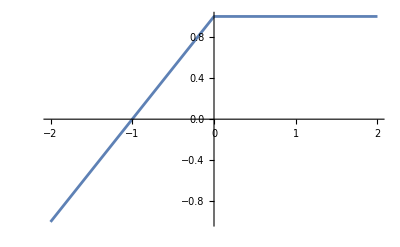

```mathematica
Clear[c,d]
k=7
Sprott[k]["fun"]/.{yp->0,ypp->0}
c=d=1
Plot[Sprott[7]["fun"]/.{yp->0,ypp->0},{y,-2,2}]
```

### Basic yJ Solver

Thinking about the basic solver.   We need to know what to do with the parameters.  In some ways this is much easier than the equilibrium computation.  We will always have values for the parameters.  The first thing I would do is build and example out of one of the problems

```mathematica
Clear[a,b,c,d]
k=2;
f[{a_,b_,c_,d_,m_}][{y_,yp_,ypp_}]={yp,ypp,NewSprott[k]["fun"]}
df[{a_,b_,c_,d_,m_}][{y_,yp_,ypp_}]={{0,1,0},{0,0,1},NewSprott[k]["der"]}
p=NewSprott[k]["par"]
u0=NewSprott[k]["IC"]
TMax=123;
{uSol,JSol}=NDSolveValue[{u'[t]==f[p][u[t]],J'[t]==df[p][u[t]].J[t],u[0]==u0,J[0]==IdentityMatrix[3]},{u,J},{t,0, TMax}]
ParametricPlot3D[uSol[t],{t,0, TMax},PlotRange->All]
JSol[1]
SingularValueList[JSol[TMax],Tolerance->0]
```

{yp,ypp,c y+d y^2-b yp+a ypp}

{{0,1,0},{0,0,1},{c+2 d y,-b,a}}

{0,2.8,1,1,50}

{-0.5,-1,1}

{InterpolatingFunction[…],InterpolatingFunction[{{0., 123.}}, <>]}

-Graphics3D-

{{0.945302,0.576548,0.389342},{-0.181881,-0.173845,0.573024},{-0.353608,-1.84523,-0.177577}}

{110.689,1.29425,0.00698033}

```mathematica
TableForm[Table[
SprottProb=NewSprott[k];
Solve[SprottProb["fun"]==0/.{yp->0,ypp->0},y],
{k,1,22}],TableHeadings->Automatic]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

General::stop: Further output of Solve::nsmet will be suppressed during this calculation.

| 1 | 2 | 3
1 | y→0 |  | 
2 | y→0 | y→-c/d | 
3 | y→(-c-√(c^2+4 d^2))/(2 d) | y→(-c+√(c^2+4 d^2))/(2 d) | 
4 | y→0 | y→-c/d | 
5 | y→d/(c-d) | y→d/(c+d) | 
6 | y→d/(c-d) | y→d/(c+d) | 
7 |  |  | 
8 |  |  | 
9 |  |  | 
10 |  |  | 
11 | Solve[-c y+d Tanh[m y]==0,y] |  | 
12 | Solve[c y-d Tanh[m y]==0,y] |  | 
13 | Solve[-c y+1/2 d (1+Tanh[m y])==0,y] |  | 
14 | y→0 |  | 
15 | y→0 |  | 
16 | Solve[-c y+d Tanh[y]==0,y] |  | 
17 | Solve[c y-d Tanh[y]==0,y] |  | 
18 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
19 | y→0 |  | 
20 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
21 | y→0 | y→-(√c)/(√d) | y→(√c)/(√d)
22 | Solve[c y+d Sin[y]==0,y] |  |

```mathematica
{c,d}={1,1};Plot[ ]
```

```mathematica
Clear[c,d]
c=d=1
Plot[Sprott[7]["fun"]/.{yp->0,ypp->0},{y,-2,2}]
```

1

-Graphics-

R

```mathematica
k=6;
Sprott[k]
```

<|fun:>-a ypp-b yp+c y+d (Abs[y]-1),par→{0.6,1,0,1,50},IC→{0,0,0}|>

What else do I need to define? What functions do I want?